### Deformation of a Beam under Load

```mathematica
Date[]
```

{2017,8,21,8,43,33.569045}

This is mostly from the FEM Programming notebook.

```mathematica
Needs["NDSolve`FEM`"]
```

A plane stress formulation as a coupled PDE.

```mathematica
Clear[u,v,x,y]
op={({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
```

In the plane stress operator, Y is Young's modulus and ν is Poisson's ratio. Those are material properties.

The beam to be deformed is of 5 units in length and 1 unit in height.

Create a mesh region with an explicit bounding box and a visualization of the mesh.

```mathematica
a=1.0;
reg1=Rectangle[{0,0},{5,2}];
(*reg2=Disk[{2.5,1},0.5];*)
```

Rectangle[{0,0},{5,2}]

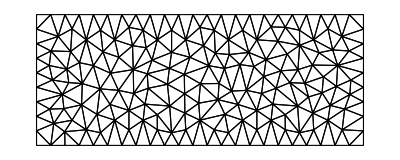

```mathematica
Ω=reg1(*RegionDifference[reg1,reg2]*)
mesh=ToElementMesh[Ω,"MaxCellMeasure"->0.05,"MeshOrder"->2,"MeshElementType"->TriangleElement];
mesh["Wireframe"]
```

```mathematica
Subscript[Γ, Du]=DirichletCondition[u[x,y]==0,x==0];
Subscript[Γ, Dv]=DirichletCondition[v[x,y]==0,x==0];
Subscript[Γ, Nv]=NeumannValue[-1,x==5];
```

```mathematica
op1=op/.{Y->10^3,ν->33/100};
```

```mathematica
{state}=NDSolve`ProcessEquations[{op1=={0,Subscript[Γ, Nv]},Subscript[Γ, Du],Subscript[Γ, Dv]},{u,v},{x,y}∈mesh]
```

{NDSolve`StateData[<SteadyState>]}

```mathematica
femdata=state["FiniteElementData"];
pded=femdata["PDECoefficientData"];
bcd=femdata["BoundaryConditionData"];
md=femdata["FEMMethodData"];
sd=state["SolutionData"][[1]];
vd=state["VariableData"];
```

Compute the discretized partial differential equation.

```mathematica
discretePDE=DiscretizePDE[pded,md,sd]
```

DiscretizedPDEData[<1386>]

Extract the system matrices.

```mathematica
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];
```

Visualize the stiffness matrix.

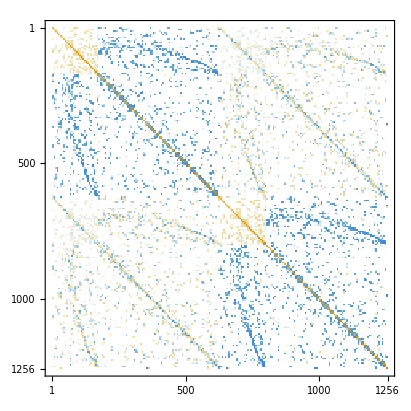

```mathematica
MatrixPlot[stiffness]
```

The visualization of the stiffness matrix shows that the structure of the underlying PDE coefficients is a system of two dependent variables. The degrees of freedom are split between the two dependent variables.

Compute how the incidents are split between the two dependent variables.

```mathematica
split=Span@@@Transpose[{Most[#+1],Rest[#]}&[md["IncidentOffsets"]]]
```

{1;;693,694;;1386}

Discretize the initialized boundary conditions.

```mathematica
discreteBCs=DiscretizeBoundaryConditions[bcd,md,sd]
```

DiscretizedBoundaryConditionData[<1386>]

Deploy the boundary conditions in place.

```mathematica
DeployBoundaryConditions[{load,stiffness},discreteBCs]
```

DeployedBoundaryConditionData[<Insert>]

Solve the system of equations.

```mathematica
Short[solution=LinearSolve[stiffness,load]]
```

{{0.},{0.},{0.},«1381»,{-0.0634911},{-0.0570311}}

Create the interpolation function with values at the nodes.

```mathematica
ufun=ElementMeshInterpolation[{mesh}, solution[[split[[1]]]]]
vfun=ElementMeshInterpolation[{mesh}, solution[[split[[2]]]]]
```

InterpolatingFunction[{{0., 5.}, {0., 2.}}, <>]

InterpolatingFunction[{{0., 5.}, {0., 2.}}, <>]

Visualize the interpolation function.

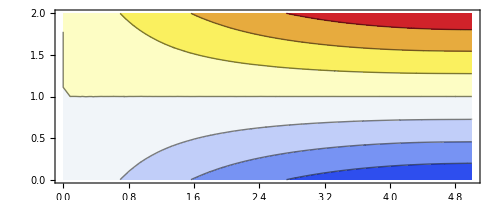

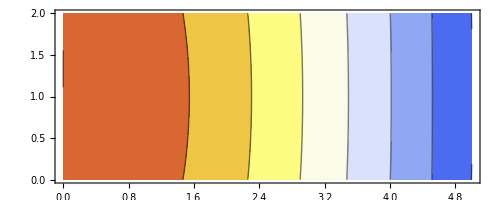

```mathematica
ContourPlot[ufun[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic]
ContourPlot[vfun[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic]
```

Visualize the deformed structure in red.

```mathematica
dmesh=ElementMeshDeformation[mesh,{ufun,vfun}]
```

ElementMesh[{{0.,5.03813},{-0.140197,2.}},{TriangleElement[<314>]}]

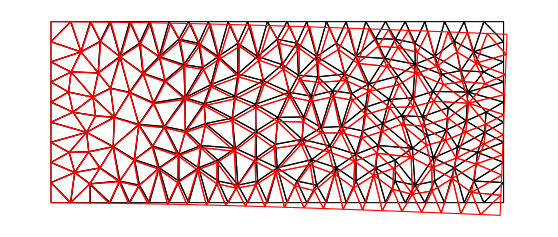

```mathematica
Show[{
mesh["Wireframe"],
dmesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]}]
```

#### Get the Elements (quite advanced stuff)

DiscretizePDE has an option to save the elements.

```mathematica
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"]
```

{SparseArray[<0>, {1386, 1}],SparseArray[<29916>, {1386, 1386}],SparseArray[<0>, {1386, 1386}],SparseArray[<0>, {1386, 1386}]}

```mathematica
ele=DiscretizePDE[pded,md,sd,"SaveFiniteElements"->True]
```

DiscretizedPDEData[<1386>]

You get a flat list of the local stiffness per element. Note, that this element contains both the value for u and v. And second you get an array of nonzero positions of the local elements. This is not relevant in this case.

```mathematica
{stiffnessElements,nonzeroPos}=ele["StiffnessElements"];
```

```mathematica
Dimensions[stiffnessElements]
```

{314,144}

```mathematica
Length[stiffnessElements]
```

314

```mathematica
dof=md["DegreesOfFreedom"];
inci=Join@@md["Incidents"];
stiffness2=AssembleMatrix[{inci,inci},stiffnessElements,{dof,dof},"Sparse"->nonzeroPos];
```

```mathematica
stiffness==stiffness2
```

True

#### Introduce the topology optimization

```mathematica
{state}=NDSolve`ProcessEquations[{op1=={0,Subscript[Γ, Nv]},Subscript[Γ, Du],Subscript[Γ, Dv]},{u,v},{x,y}∈mesh]
femdata=state["FiniteElementData"];
pded=femdata["PDECoefficientData"];
bcd=femdata["BoundaryConditionData"];
md=femdata["FEMMethodData"];
sd=state["SolutionData"][[1]];
vd=state["VariableData"];
discretePDE=DiscretizePDE[pded,md,sd]
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];
discreteBCs=DiscretizeBoundaryConditions[bcd,md,sd]
ele=DiscretizePDE[pded,md,sd,"SaveFiniteElements"->True]
{stiffnessElements,nonzeroPos}=ele["StiffnessElements"];
```

{NDSolve`StateData[<SteadyState>]}

DiscretizedPDEData[<1386>]

DiscretizedBoundaryConditionData[<1386>]

DiscretizedPDEData[<1386>]

```mathematica
density=Table[ρ[i],{i,1,Length@stiffnessElements}];
modifiedElements=density*stiffnessElements;
```

```mathematica
dof=md["DegreesOfFreedom"];
inci=Join@@md["Incidents"];
stiffness2=AssembleMatrix[{inci,inci},stiffnessElements,{dof,dof},"Sparse"->nonzeroPos];
modifiedstiffness2=AssembleMatrix[{inci,inci},modifiedElements,{dof,dof},"Sparse"->nonzeroPos];
```

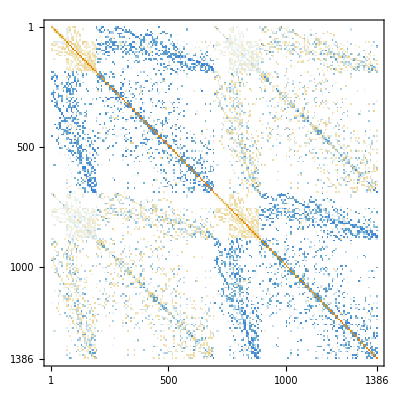
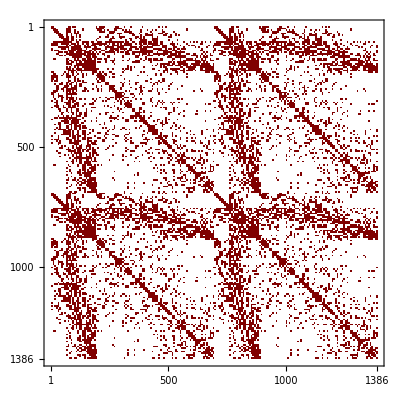
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MatrixPlot[stiffness],MatrixPlot[stiffness2],MatrixPlot[modifiedstiffness2]}
```

```mathematica
displacement=Table[δ[i],{i,1,Length[stiffness2]}];
coords=mesh["Coordinates"];
elems=mesh["MeshElements"];
```

```mathematica
DeployBoundaryConditions[{load,stiffness},discreteBCs]
DeployBoundaryConditions[{load,stiffness2},discreteBCs]
DeployBoundaryConditions[{load,modifiedstiffness2},discreteBCs]
```

DeployedBoundaryConditionData[<Insert>]

DeployedBoundaryConditionData[<Insert>]

DeployedBoundaryConditionData[<Insert>]

```mathematica
loadF=Flatten[load];
```

```mathematica
square=Apply[0.5*((coords[[#3,1]]-coords[[#1,1]])*(coords[[#3,2]]+coords[[#1,2]])-(coords[[#2,1]]-coords[[#1,1]])*(coords[[#2,2]]+coords[[#1,2]])-(coords[[#3,1]]-coords[[#2,1]])*(coords[[#3,2]]+coords[[#2,2]]))&]/@elems[[1,1,1;;Length[stiffnessElements],1;;3]];
```

```mathematica
goalFunction=displacement.modifiedstiffness2.displacement;
massEquation=∑_(k=1)^Length[square] square⟦k⟧ density⟦k⟧≤(∑_(k=1)^Length[square] square⟦k⟧) 1;
densityEq=Thread[(0.0≤#1≤1.5&)[density]];
equation=Table[modifiedstiffness2⟦i⟧.displacement==loadF⟦i⟧,{i,1,Length[displacement]}];
```

```mathematica
sysOfEq=Flatten[{goalFunction,massEquation,equation,densityEq}];
sysOfEq//Length
variables=Flatten[{density,displacement}];
variables//Length
```

1702

1700

```mathematica
initDis=Thread[{#,0}&[displacement]];
initDen=Thread[{#,0.5}&[density]];
initCond=Flatten[{initDen,initDis},1];
```

```mathematica
resultFMin=Quiet[FindMinimum[sysOfEq,initCond]];//AbsoluteTiming
```

{28.4301,Null}

```mathematica
minimizedDen=density/.resultFMin[[2]];
```

```mathematica
Total[#]/Length[#]&@minimizedDen
```

0.999455

```mathematica
Sum[minimizedDen[[k]]*square[[k]],{k,1,Length[square]}]/Sum[square[[k]],{k,1,Length[square]}]
```

1.

```mathematica
normModified2=Normal[modifiedstiffness2];
```

```mathematica
minimizedstiffness2=normModified2/.resultFMin[[2]]
```

{1}
 |  |  |  |

```mathematica
minimizedstiffness2[[1,1]]
```

1.

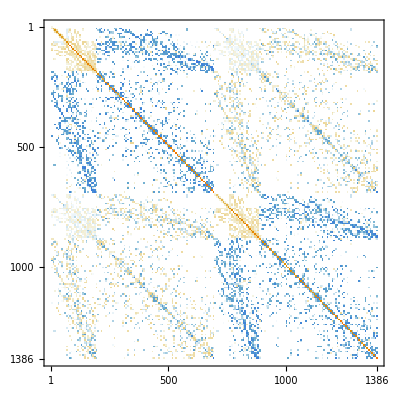
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MatrixPlot[stiffness2],MatrixPlot[stiffness2],MatrixPlot[minimizedstiffness2]}
```

Solution with optimized stiffness matrix

```mathematica
Short[solution1=LinearSolve[stiffness,load]]
Short[solution2=LinearSolve[stiffness2,load]]
Short[solution3=LinearSolve[minimizedstiffness2,load]]
```

{{0.},{0.},{0.},«1381»,{-0.190473},{-0.171093}}

{{0.},{0.},{0.},«1381»,{-0.190473},{-0.171093}}

{{-3.88311×10^-14},«1384»,{-0.127939}}

```mathematica
ufun=ElementMeshInterpolation[{mesh}, solution[[split[[1]]]]]
vfun=ElementMeshInterpolation[{mesh}, solution[[split[[2]]]]]
ufun1=ElementMeshInterpolation[{mesh}, solution3[[split[[1]]]]]
vfun1=ElementMeshInterpolation[{mesh}, solution3[[split[[2]]]]]
```

InterpolatingFunction[{{0., 5.}, {0., 2.}}, <>]

InterpolatingFunction[{{0., 5.}, {0., 2.}}, <>]

InterpolatingFunction[{{0., 5.}, {0., 2.}}, <>]

«1 more identical outputs»

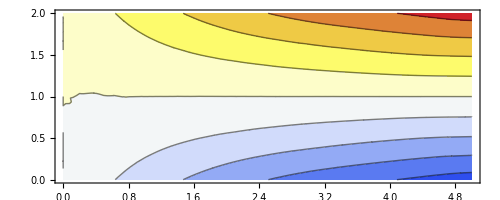
{-Graphics-,-Graphics-}

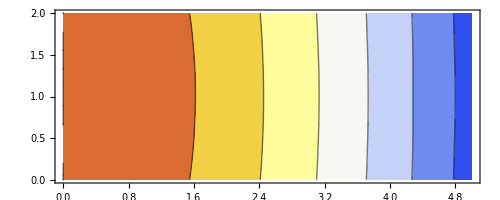
{-Graphics-,-Graphics-}

```mathematica
{ContourPlot[ufun[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic],ContourPlot[ufun1[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic]}
{ContourPlot[vfun[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic],
ContourPlot[vfun1[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic]}
```

```mathematica
dmesh=ElementMeshDeformation[mesh,{ufun,vfun}]
dmesh2=ElementMeshDeformation[mesh,{ufun1,vfun1}]
```

ElementMesh[{{0.,5.03813},{-0.140197,2.}},{TriangleElement[<314>]}]

ElementMesh[{{-1.36709×10^-13,5.0895},{-0.325757,2.}},{TriangleElement[<314>]}]

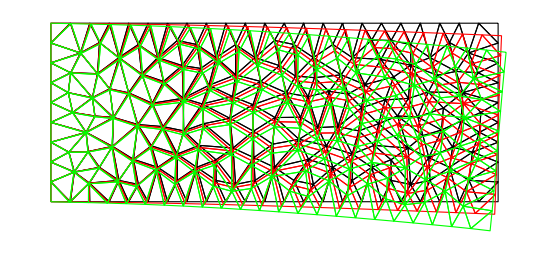

```mathematica
Show[{
mesh["Wireframe"],
dmesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]],
dmesh2["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Green],FaceForm[]]]]
}]
```

```mathematica
polys=Polygon[#]&/@(
Apply[{coords[[#1]],coords[[#2]],coords[[#3]]}&]/@elems[[1,1,1;;Length[square],1;;3]]);
```

```mathematica
Length[density]
```

314

```mathematica
Length[square]
```

314

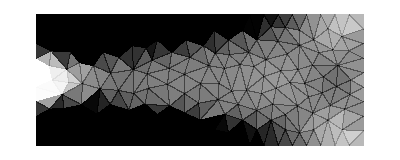

```mathematica
maxden=Max[minimizedDen];
denpolys=Transpose[{minimizedDen/maxden,polys}];
filteredpolys=Select[denpolys,#[[1]]>0.0&];
opacityfiltered=Replace[#,{x_,y_}:>{Opacity[x],y}]&/@filteredpolys;
Graphics[opacityfiltered]
```

```mathematica
elems[[1,1,1,1;;3]]
```

{1,11,2}

### Without AssembleMatrix

```mathematica
matrixAssembly[ values_,pos_,dim_]:=Block[{matrix,p},
System`SetSystemOptions[ "SparseArrayOptions"->{"TreatRepeatedEntries"->1}];
matrix=SparseArray[ pos->Flatten[ values],dim];
System`SetSystemOptions[ "SparseArrayOptions"->{"TreatRepeatedEntries"->0}];
Return[ matrix]]
```

```mathematica
inci=Join@@md["Incidents"];
```

```mathematica
pos=Flatten[Extract[#,nonzeroPos["NonzeroPositions"]]&/@Map[ Outer[ List,#,#]&,inci],1];
```

In this coupled PDE there are no zero elements. Further down there is an example op that has zero positions

```mathematica
MatrixForm[nonzeroPos]
```

(1 | 2 | 3 | 4 | 17 | 18 | 19 | 20
5 | 6 | 7 | 8 | 21 | 22 | 23 | 24
9 | 10 | 11 | 12 | 25 | 26 | 27 | 28
13 | 14 | 15 | 16 | 29 | 30 | 31 | 32
33 | 34 | 35 | 36 | 49 | 50 | 51 | 52
37 | 38 | 39 | 40 | 53 | 54 | 55 | 56
41 | 42 | 43 | 44 | 57 | 58 | 59 | 60
45 | 46 | 47 | 48 | 61 | 62 | 63 | 64)

The local stiffness elements are organized in a way to make efficient use of the nonzero positions for matrix assembly. Here is a way to ‘undo’ that ordering:

```mathematica
ord=Ordering[DeleteCases[Ordering[nonzeroPos//Normal//Flatten],0]];
```

```mathematica
ordStiffEle=stiffnessElements[[All,ord]];
```

```mathematica
s3=matrixAssembly[ordStiffEle,pos,md["DegreesOfFreedom"]]
```

SparseArray[…]

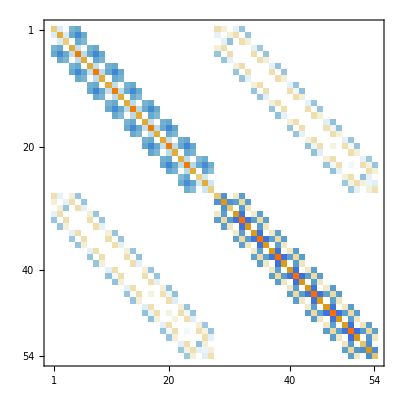
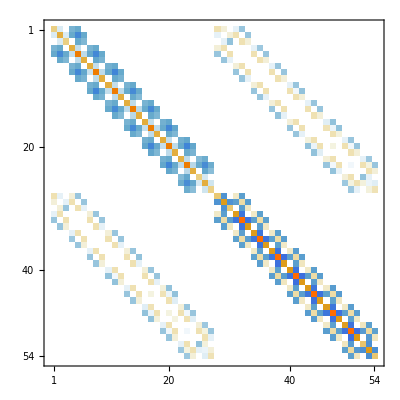

```mathematica
MatrixPlot/@{(s1=discretePDE["StiffnessMatrix"]),s3}
```

```mathematica
s1==s3
```

True

The following is an example of an op for when there are zeros from local elements, these are never inserted into the global stiffness matrix - this is pretty advanced stuff:

```mathematica
(*Clear[u,v,x,y]
op={({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};*)
```

### Results

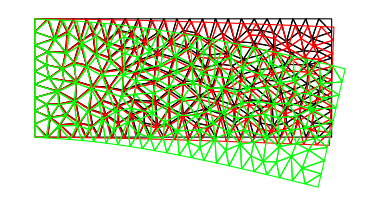
```mathematica
0.75
-Graphics-
```